#### Let' s talk about putting complex images on an e - paper display. The panels I' m using here only support two colors on a white background. We' ll start by making some images with appropriate colors, and importing some others using ColorQuantize to color reduce them.

```mathematica
cosplot := Plot[Cos[x],{x,0,8},ImageSize->{212,104},PlotStyle->{Red},TicksStyle->{{Black,Directive[FontOpacity->0]},{Black,Directive[FontOpacity->0]}},ImagePadding->None,ImageMargins->0]
```

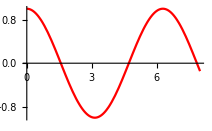

```mathematica
cosplot
```

```mathematica
ARES := ColorQuantize[ImageResize[ImageCrop[Import["~/badge/ares3.png"]],{75,70}],{White,Black,Red}]
```

```mathematica
ARRL := ColorQuantize[ImageResize[Import["~/badge/arrl.png"],{30,70}],{White,Black}]
```

```mathematica
Skywarn := ColorQuantize[ImageResize[Import["~/badge/skywarn.jpg"],{45,55}],{White,Black,Red}]
```

```mathematica
{ARRL,ARES,Skywarn}
```

{-Graphics-,-Graphics-,-Graphics-}

#### We' ll also need some rasterized text to make the badge look interesting.

```mathematica
callsign := Graphics[Text[Style["K0SIN",FontSize->30,FontFamily->"Century Schoolbook L"]]]
```

```mathematica
name := Graphics[Text[Style["Christopher Smith",FontSize->14,FontFamily->"Century Schoolbook L"]]]
```

#### Now we build an image consisting of multiple of the above elements.

```mathematica
tag = ColorQuantize[RemoveAlphaChannel[ImageCompose[#,name,Scaled[{.33,.6}]] & @ImageCompose[#,callsign,Scaled[{.28,.8}]] & @ImageCompose[#,ARES,Scaled[{.7,.35}]] & @ImageCompose[cosplot,Skywarn,Scaled[{.9,.25}]],White],{White,Black,Red}]
```

-Graphics-

#### Now split the red from the black, and rotate the images so that they' re oriented correctly for the display.

```mathematica
blackchannel =ImageRotate[Binarize[ColorReplace[tag,Red->White]]];
redchannel = ImageRotate[Binarize[ColorReplace[tag,Black->White]]];
```

```mathematica
{redchannel,blackchannel}
```

{-Graphics-,-Graphics-}

#### If we want to write an include file which describes the image we' ve just made in a C - style set of constants like the Heltec demo code did, we can do the following :

```mathematica
blackcode = "const unsigned char IMAGE_BLACK[] PROGMEM = " <>ToString[FromDigits[#,2] &/@Partition[Flatten[ImageData[blackchannel,"Bit"]],8]] <> ";";
redcode = "const unsigned char IMAGE_RED[] PROGMEM = " <>ToString[FromDigits[#,2] &/@Partition[Flatten[ImageData[redchannel,"Bit"]],8]] <> ";";
outfile = OpenWrite["~/badge/imagedata-new.cpp"];
WriteString[outfile,"#include \"imagedata.h\">\n"];
WriteString[outfile,"#include <avr/pgmspace.h>\n"];
WriteString[outfile,blackcode <> "\n"];
WriteString[outfile,redcode <> "\n\n"];
Close[outfile]
```

#### If we' d rather write the raster out to a raw image which can be loaded into memory by our sketch from SPIFFS, we can do this instead :

```mathematica
outfile = OpenWrite["~/badge/example.img",BinaryFormat->True];
BinaryWrite[outfile,FromDigits[#,2] &/@Partition[Flatten[ImageData[blackchannel,"Bit"]],8]];
BinaryWrite[outfile,FromDigits[#,2] &/@Partition[Flatten[ImageData[redchannel,"Bit"]],8]];
Close[outfile]
```